```mathematica
Clear[a]
a[c_]:=a[c]=Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/total_100_lead_15_device_50_length_100_up_60_.dat"][[c]]
```

```mathematica
mean[c_]:={a[c][[1]],Mean[Join[{ToExpression[StringReplace[a[c][[2]],","->"}"]][[1]]},Table[ToExpression[StringReplace[a[c][[x]],","->""]],{x,3,1000}]]]}
```

```mathematica
xxx=Monitor[Table[mean[c],{c,201}],c]
```

{{0.,0.648828},{0.01,1.29599},{0.02,0.762987},{0.03,0.635317},{0.04,0.528191},{0.05,0.321883},{0.06,0.250337},{0.07,0.207479},{0.08,0.203881},{0.09,0.311731},{0.1,0.312717},{0.11,0.275698},{0.12,0.273703},{0.13,0.203598},{0.14,0.34317},{0.15,0.515882},{0.16,0.393894},{0.17,0.389723},{0.18,0.322697},{0.19,0.385929},{0.2,0.403633},{0.21,0.207213},{0.22,0.419261},{0.23,0.482416},{0.24,0.400705},{0.25,0.440343},{0.26,0.499676},{0.27,0.297759},{0.28,0.648833},{0.29,0.522724},{0.3,0.697593},{0.31,0.872727},{0.32,0.663714},{0.33,0.933213},{0.34,0.732428},{0.35,0.994749},{0.36,0.816039},{0.37,0.843308},{0.38,0.755266},{0.39,0.733877},{0.4,0.672204},{0.41,0.807938},{0.42,0.806852},{0.43,1.10174},{0.44,1.44291},{0.45,1.44517},{0.46,1.68999},{0.47,1.7706},{0.48,1.74841},{0.49,1.778},{0.5,1.82237},{0.51,1.77452},{0.52,1.77852},{0.53,1.75718},{0.54,1.82522},{0.55,1.58865},{0.56,1.74178},{0.57,1.5607},{0.58,1.44476},{0.59,1.36796},{0.6,1.06816},{0.61,1.21478},{0.62,1.17409},{0.63,1.10846},{0.64,1.2},{0.65,1.28114},{0.66,1.6742},{0.67,1.32825},{0.68,1.56016},{0.69,1.75076},{0.7,2.15997},{0.71,2.32741},{0.72,2.42353},{0.73,2.45412},{0.74,2.5701},{0.75,2.61655},{0.76,2.65763},{0.77,2.78179},{0.78,2.79072},{0.79,2.76917},{0.8,2.79842},{0.81,2.71363},{0.82,2.87301},{0.83,2.67686},{0.84,2.19703},{0.85,1.82442},{0.86,2.51637},{0.87,2.74699},{0.88,3.00189},{0.89,3.18076},{0.9,3.21164},{0.91,3.31625},{0.92,3.46906},{0.93,3.48928},{0.94,3.62144},{0.95,3.44446},{0.96,2.40315},{0.97,2.67882},{0.98,3.10668},{0.99,3.18457},{1.,3.38708},{1.01,3.70011},{1.02,3.76535},{1.03,3.93187},{1.04,4.07252},{1.05,4.11922},{1.06,4.1369},{1.07,3.82177},{1.08,3.60057},{1.09,3.53618},{1.1,3.53867},{1.11,3.57046},{1.12,3.61977},{1.13,3.69828},{1.14,3.71825},{1.15,3.78649},{1.16,3.85296},{1.17,3.85502},{1.18,3.84985},{1.19,3.77833},{1.2,3.63172},{1.21,3.50873},{1.22,3.46894},{1.23,3.49509},{1.24,3.47051},{1.25,3.51426},{1.26,3.52465},{1.27,3.52005},{1.28,3.55713},{1.29,3.5551},{1.3,3.52448},{1.31,3.43113},{1.32,3.25333},{1.33,3.09265},{1.34,2.951},{1.35,2.83846},{1.36,2.6929},{1.37,2.55003},{1.38,2.31161},{1.39,1.84048},{1.4,2.29948},{1.41,2.54547},{1.42,2.74704},{1.43,2.85327},{1.44,2.89785},{1.45,2.95507},{1.46,2.99079},{1.47,3.06907},{1.48,3.12104},{1.49,3.1847},{1.5,3.24626},{1.51,3.33284},{1.52,3.32957},{1.53,3.38095},{1.54,3.43129},{1.55,3.40272},{1.56,3.38454},{1.57,3.33059},{1.58,3.25698},{1.59,3.29388},{1.6,3.29908},{1.61,3.32488},{1.62,3.33025},{1.63,3.33473},{1.64,3.33526},{1.65,3.34784},{1.66,3.3229},{1.67,3.2929},{1.68,3.18647},{1.69,3.09574},{1.7,3.02991},{1.71,2.96485},{1.72,2.91877},{1.73,2.83264},{1.74,2.74039},{1.75,2.57578},{1.76,2.20434},{1.77,1.90295},{1.78,2.12681},{1.79,2.28326},{1.8,2.32185},{1.81,2.38232},{1.82,2.46749},{1.83,2.57478},{1.84,2.59132},{1.85,2.67015},{1.86,2.73178},{1.87,2.78939},{1.88,2.80039},{1.89,2.83617},{1.9,2.82766},{1.91,2.80984},{1.92,2.76659},{1.93,2.7941},{1.94,2.79117},{1.95,2.82276},{1.96,2.81342},{1.97,2.82153},{1.98,2.83722},{1.99,2.81604},{2.,2.82285}}

```mathematica
Export["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_device_50_length_100_up_60_.dat",xxx]
```

~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_device_50_length_100_up_60_.dat

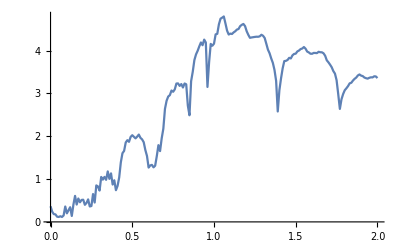

```mathematica
ListPlot[%66,Joined->True]
```

```mathematica
%26[[4]]
```

0.16763028728366777,

```mathematica
ToExpression[StringReplace[%26[[2]],","->""]]
```

ToExpression::sntxi: Incomplete expression; more input is needed .

$Failed